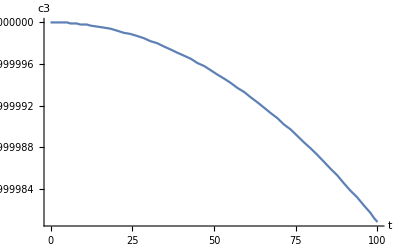

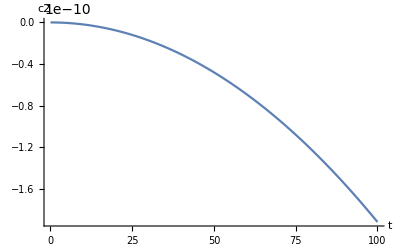

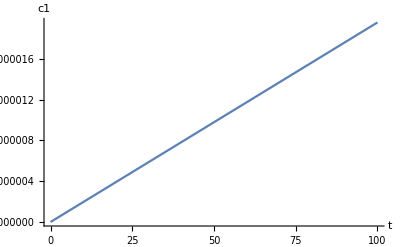

```mathematica
h=6.62607015*10^(-34);
ϵ0=8.8541878128*10^(-12);
e=1.6*10^(-19);
a0=5.29*10^(-11);
c=3*10^8;
ℏ=h/(2 π);
V=1;

γ32=ω32^3 d32^2/(6 π ϵ0 ℏ c^3);
γ31=ω31^3 d31^2/(6 π ϵ0 ℏ c^3);
γ21=ω21^3 d21^2/(6 π ϵ0 ℏ c^3);


Ω=0;
d31=e a0;
d21=e a0;
d32=0;

ω31=1;
ω21=1;
ω32=1;
ωk=1;

μ31=ωk-ω31;
μ21=ωk-ω21;


α=0;(* alpha is angle between polarization of photon (kλ) and dipole moment of transition j to i *)
g31=ω31 d31 Sqrt[ℏ/(2 ϵ0 ωk V)] Cos[α]/ℏ;
g21=ω21 d21 Sqrt[ℏ/(2 ϵ0 ωk V)] Cos[α]/ℏ;

(* Constants *)
ϕp=0;
ϕc=π/2;
θ=0;

(*Vacuum*)

eqs={
c3'[t]==-Ω c2[t] Exp[-I ϕc]-g31 c1[t]Exp[-I μ31 t],
c2'[t]==Ω c3[t] Exp[I ϕc]-g21 c1[t]Exp[-I μ21 t],
c1'[t]==g31 c3[t] Exp[I μ31 t]+g21 c2[t] Exp[I μ21 t],
c3[0]==Cos[θ],
c2[0]==Sin[θ]Exp[I ϕp],
c1[0]==0
};

vars={c1[t],c2[t],c3[t]};
sol=DSolve[eqs,vars,t];
(*
vars={c1,c2,c3};
sol=NDSolve[eqs,vars,{t,0,100}];
*)
Plot[Evaluate[c3[t]/.sol],{t,0,100},PlotRange->All,AxesLabel->{"t","c3"}]
Plot[Evaluate[c2[t]/.sol],{t,0,100},PlotRange->All,AxesLabel->{"t","c2"}]
Plot[Evaluate[c1[t]/.sol],{t,0,100},PlotRange->All,AxesLabel->{"t","c1"}]
```